# Project Euler Problem 201

For any set A of numbers, let sum(A) be the sum of the elements of A.
Consider the set B = {1,3,6,8,10,11}.
There are 20 subsets of B containing three elements, and their sums are:

sum({1,3,6}) = 10,
sum({1,3,8}) = 12,
sum({1,3,10}) = 14,
sum({1,3,11}) = 15,
sum({1,6,8}) = 15,
sum({1,6,10}) = 17,
sum({1,6,11}) = 18,
sum({1,8,10}) = 19,
sum({1,8,11}) = 20,
sum({1,10,11}) = 22,
sum({3,6,8}) = 17,
sum({3,6,10}) = 19,
sum({3,6,11}) = 20,
sum({3,8,10}) = 21,
sum({3,8,11}) = 22,
sum({3,10,11}) = 24,
sum({6,8,10}) = 24,
sum({6,8,11}) = 25,
sum({6,10,11}) = 27,
sum({8,10,11}) = 29.

Some of these sums occur more than once, others are unique.
For a set A, let U(A,k) be the set of unique sums of k-element subsets of A, in our example we find U(B,3) = {10,12,14,18,21,25,27,29} and sum(U(B,3)) = 156.

Now consider the 100-element set S = {12, 22, ... , 1002}.
S has 100891344545564193334812497256 50-element subsets.

Determine the sum of all integers which are the sum of exactly one of the 50-element subsets of S, i.e. find sum(U(S,50)).

```mathematica
setB={1,3,6,8,10,11}
```

{1,3,6,8,10,11}

```mathematica
sumU[set_,order_]:=Composition[
Total,
Cases[#,{s_,1}:> s]&,
Tally,
Total/@#&,
Subsets[#,{order}]&
][set]
```

```mathematica
sumU[setB,1]
sumU[setB,2]
sumU[setB,3]
sumU[setB,4]
sumU[setB,5]
sumU[setB,6]
```

39

127

156

224

195

39

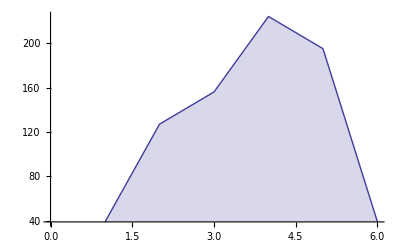

```mathematica
With[{max=Length[setB]},ListPlot[Table[sumU[setB,n],{n,1,max}],Filling-> Bottom,Joined-> True]]
```

```mathematica
setS=Table[n^2,{n,100}];
```

```mathematica
Composition[
Total,
Cases[#,{s_,1}:> s]&,
Tally,
Total/@#&,
Subsets[#,{5}]&
][setS]
```

45263176

```mathematica
setS
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400,441,484,529,576,625,676,729,784,841,900,961,1024,1089,1156,1225,1296,1369,1444,1521,1600,1681,1764,1849,1936,2025,2116,2209,2304,2401,2500,2601,2704,2809,2916,3025,3136,3249,3364,3481,3600,3721,3844,3969,4096,4225,4356,4489,4624,4761,4900,5041,5184,5329,5476,5625,5776,5929,6084,6241,6400,6561,6724,6889,7056,7225,7396,7569,7744,7921,8100,8281,8464,8649,8836,9025,9216,9409,9604,9801,10000}

```mathematica
Subsets[setB,{2}]
```

{{1,3},{1,6},{1,8},{1,10},{1,11},{3,6},{3,8},{3,10},{3,11},{6,8},{6,10},{6,11},{8,10},{8,11},{10,11}}

```mathematica
Subsets[setB,{3}]
```

{{1,3,6},{1,3,8},{1,3,10},{1,3,11},{1,6,8},{1,6,10},{1,6,11},{1,8,10},{1,8,11},{1,10,11},{3,6,8},{3,6,10},{3,6,11},{3,8,10},{3,8,11},{3,10,11},{6,8,10},{6,8,11},{6,10,11},{8,10,11}}